```mathematica
CleanSlate[];
```

Remove::rmnsm: There are no symbols matching ""x$"".

contexts purged: {Global`}

approximate kernel memory recovered: 0 Kb

```mathematica
sol1 = Solve[{x^3-2 x y + y^2==4,x+4 x y+3 y^2==7},{x,y}, Reals];
```

```mathematica
sol1[[1]]
```

{x→(7-3 Root[-339+62 #1+744 #1^2+462 #1^3-285 #1^4-160 #1^5+27 #1^6&,1]^2)/(1+4 Root[-339+62 #1+744 #1^2+462 #1^3-285 #1^4-160 #1^5+27 #1^6&,1]),y→Root[-339+62 #1+744 #1^2+462 #1^3-285 #1^4-160 #1^5+27 #1^6&,1]}

```mathematica
sol1//N
```

{{x→0.305073,y→-1.71103},{x→1.79169,y→0.583978},{x→-0.273573,y→1.75012},{x→-4.83056,y→7.0038}}

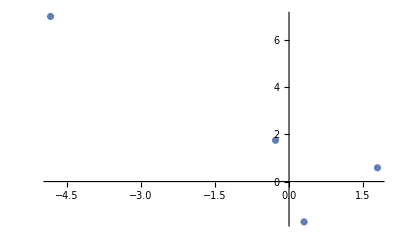

```mathematica
ListPlot[{x,y}/.sol1]
```

```mathematica
f[x_]:=x^3-x-1
```

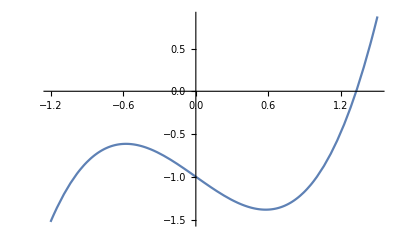

```mathematica
Plot[f[x],{x,-1.2,1.5}]
```

```mathematica
Roots[f[x]==0,x]//N
```

x==1.32472||x==-0.662359+0.56228 ⅈ||x==-0.662359-0.56228 ⅈ

```mathematica
NSolve[f[x]==0,x,Reals]
```

{{x→1.32472}}

```mathematica
DeleteDuplicates[NSolve[f[x]==0,x,Reals]]
```

{{x→1.32472}}